```mathematica
NotebookEvaluate["D:\\Documents\\GitHubVisualStudio\\CATSPDEs project\\CATSPDEs\\sln\\Tools\\Mathematica\\triangulation.nb"]
```

```mathematica
NotebookEvaluate["D:\\Documents\\GitHubVisualStudio\\CATSPDEs project\\CATSPDEs\\sln\\Tools\\Mathematica\\FEinterpolants.nb"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

## mesh levels data

```mathematica
lvl=Import@"meshLevels.dat"//First;
ssz=Import@"systemSizes.dat"//First;
nnz=Import@"nnzeros.dat"//First;
l=Length@lvl;
```

```mathematica
ssz
```

{53,185,689,2657,10433,41345,164609,656897,2624513}

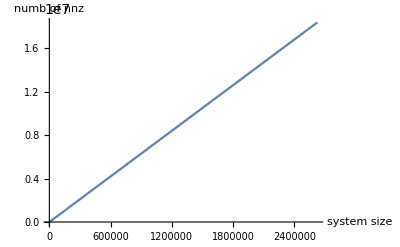

```mathematica
ListLinePlot[Table[{ssz[[i]],nnz[[i]]},{i,l}],
AxesLabel->{"system size","numb of nnz"},
PlotRange->All
]
```

## multigrid complexity

```mathematica
wcycle={.003,.012,.042,.158,.587,2.388,11.661,51.855,288.801}/10.;
vcycle={.004,.011,.03,.111,.401,1.77,8.616,36.861,173.568}/10.;
```

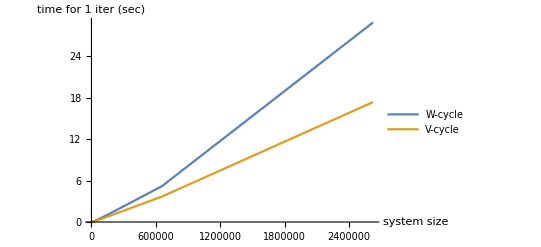

```mathematica
ListLinePlot[{Table[{ssz[[i]],wcycle[[i]]},{i,l}],Table[{ssz[[i]],vcycle[[i]]},{i,l}]},
PlotLegends->{"W-cycle","V-cycle"},
AxesLabel->{"system size","time for 1 iter (sec)"},
PlotRange->All
]
```

## CG vs MG vs PCG

```mathematica
cg={.011,.015,.023,.132,.632,4.934,44.987,361.045,∞};
pcg={.023,.032,.046,.091,.264,1.049,4.503,26.193,101.081};
mgv={.022,.044,.58,.101,.263,1.152,4.838,20.112,101.144};
mgw={.027,.038,.52,.129,.361,1.383,6.414,27.715,116.88};
```

time that solver needs in order to anihilate residual, || r || < 10^-8 versus system size
for MG we used V-cycle and W-cycle, SOR as a smoother (ν = 10, ω = 1.5)
for PCG we used MG V-cycle from above as an inner solver

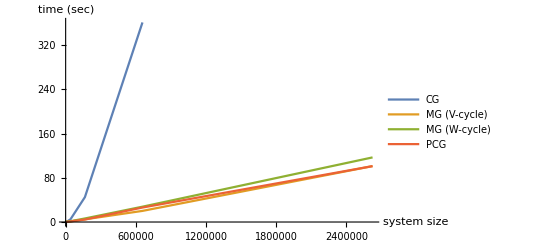

```mathematica
ListLinePlot[{Table[{ssz[[i]],cg[[i]]},{i,l}],Table[{ssz[[i]],mgv[[i]]},{i,l}],Table[{ssz[[i]],mgw[[i]]},{i,l}],Table[{ssz[[i]],pcg[[i]]},{i,l}]},
PlotLegends->{"CG","MG (V-cycle)","MG (W-cycle)","PCG"},
AxesLabel->{"system size","time (sec)"},
PlotRange->All
]
```

## soln

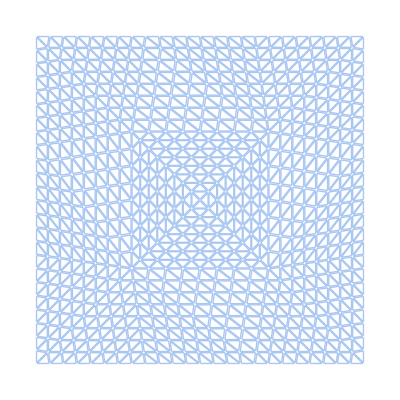

```mathematica
ℳ=import@"mesh.nt";
highlight[ℳ,{}]
```

```mathematica
ξ=Import["xi.dat"]//First;
```

```mathematica
Pξ=interpolantOfξ[ξ,ΔP1L,ℳ];
```

```mathematica
Plot3D[{Pξ[x,y]},{x,y}∈region@ℳ]
```

-Graphics3D-

## res history

```mathematica
cg=Import@"CG.dat"//First;
gs=Import@"GS.dat"//First;
ja=Import@"Jacobi.dat"//First;
mg=Import@"MG.dat"//First;
pcg=Import@"PCG.dat"//First;
```

```mathematica
Length@mg
```

100

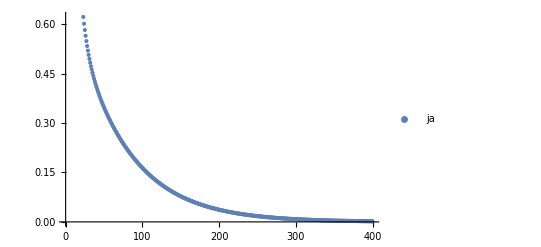

```mathematica
ListPlot[{gs,ja},PlotLegends-> {"gs","ja"}]
```

```mathematica
mg//Last
```

0.000456177

```mathematica
rja=Table[ja[[i]]/ja[[i+1]],{i,Length@ja-1}];
```

```mathematica
rmg=Table[mg[[i]]/mg[[i+1]],{i,Length@mg-1}];
```

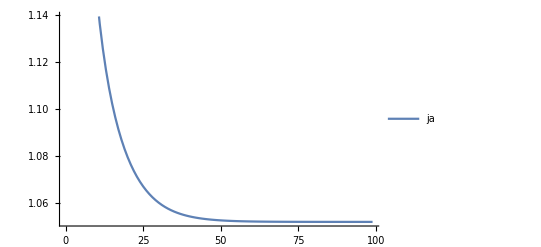

```mathematica
ListLinePlot[{rmg},PlotLegends->{"ja","mg"}]
```

```mathematica
mg[[51]]/mg[[52]]
```

1.05253

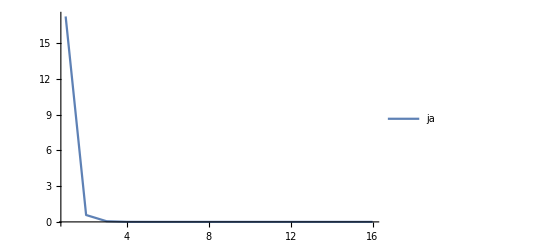

```mathematica
ListLinePlot[{pcg},PlotRange->All,PlotLegends-> {"ja","cg","mg"}]
```

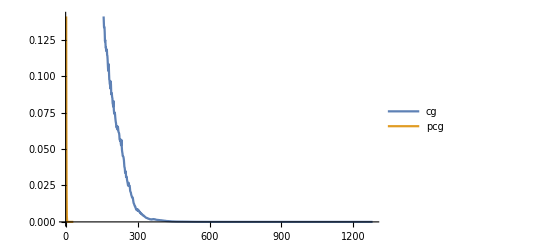

```mathematica
ListLinePlot[{cg,pcg},PlotLegends-> {"cg","pcg"}]
```

```mathematica
Length@cg
Length@pcg
```

1280

413

```mathematica
cg//Last
```

1.02579×10^-16

```mathematica
pcg//Last
```

8.04205×10^-8

```mathematica
cgt={.023,.257,1.873,15.028}
pcgt={.6,3.6,25.9,188.5}
```

{0.023,0.257,1.873,15.028}

{0.6,3.6,25.9,188.5}

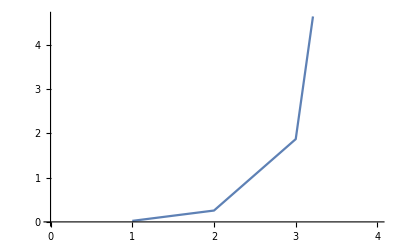

```mathematica
ListLinePlot@cgt
```

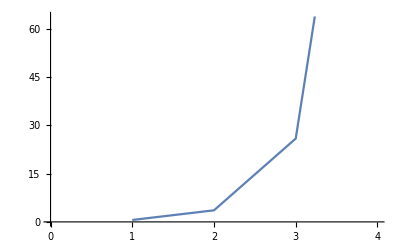

```mathematica
ListLinePlot@pcgt
```